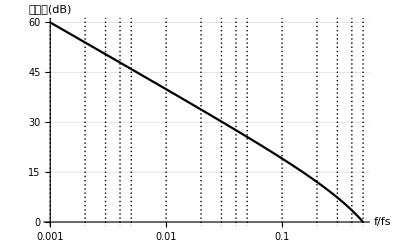

```mathematica
gzoh[Ω_]:=Abs[Sinc[Ω/2]];
gdif[f_,fs_]:=gzoh[2π f/fs]/gzoh[2π(fs-f)/fs];
LogLinearPlot[20*Log10[gdif[f,1]],{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.001,0.5+0.00001},{0,60}},GridLines->{{0.001,0.002,0.003,0.004,0.005,0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style[":589e:76ca:5dee(dB)",FontFamily->"Times",FontSize->12]}]
```

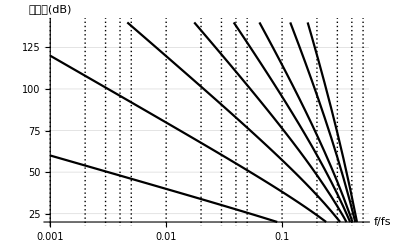

-Graphics-

```mathematica
gdifdb[fn_]:=20*Log10[gdif[fn,1]];
gd2[fn_,o_]:=gdif[fn,1]*((1-fn)/fn)^o;
gd2db[fn_,o_]:=gdifdb[fn]+(Log10[(1-fn)/fn]*20*o);
LogLinearPlot[20*Log10[gd2[f,{0,1,2,3,4,5,7,9}]],{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.001,0.5+0.00001},{20,140}},GridLines->{{0.001,0.002,0.003,0.004,0.005,0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["信镜比(dB)",FontFamily->"Times",FontSize->12]}]
LogLinearPlot[gd2db[f,{0,1,2,3,4,5,7,9}],{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.001,0.5+0.00001},{20,140}},GridLines->{{0.001,0.002,0.003,0.004,0.005,0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["信镜比(dB)",FontFamily->"Times",FontSize->12]}]
```

```mathematica
o
```

```mathematica
gzoh2[Ω_]:=Abs[Sin[Ω/2]/(Ω/2)];
FullSimplify[gzoh2[2π f/fs]/gzoh2[2π(fs-f)/fs]]
```

Abs[1-fs/f]